# Even MCPP Algorithm

Conditions

Strongly connected

```mathematica
PacletInstall[ResourceObject["PeterBurbery/MixedGraphs"]]
```

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

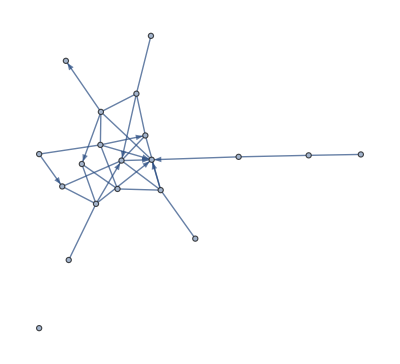

```mathematica
RandomMixedGraph[{20,30},0.5]
```

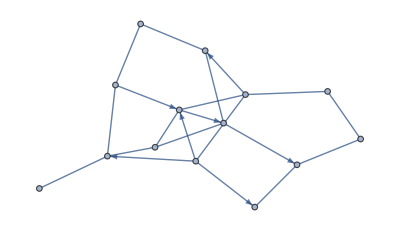

```mathematica
First[TakeLargestGraphComponentBy[RandomMixedGraph[{20,30},0.5]]]
```

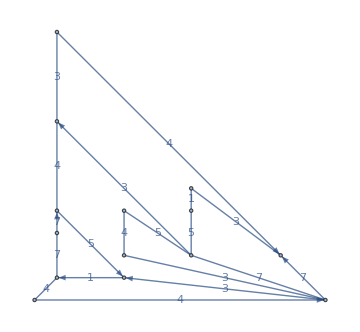

```mathematica
First[TakeLargestGraphComponentBy[RandomWeightedMixedGraph[{20,24},0.5,RandomInteger[{1,7}]&,EdgeLabels->"EdgeWeight",GraphLayout->"PlanarEmbedding",ImageSize->Medium]]]
```

## Conditions

Strongly connected

```mathematica
ConnectedGraphQ[First[TakeLargestGraphComponentBy[RandomWeightedMixedGraph[{20,24},0.5,RandomInteger[{1,7}]&,EdgeLabels->"EdgeWeight",GraphLayout->"PlanarEmbedding",ImageSize->Medium]]]]
```

True

```mathematica
VertexDegree[First[TakeLargestGraphComponentBy[RandomWeightedMixedGraph[{7,21},0.5,RandomInteger[{1,7}]&,EdgeLabels->"EdgeWeight",GraphLayout->"PlanarEmbedding",ImageSize->Medium]]]]
```

{6,6,5,4,5,3,3}

```mathematica
EdgeCount[CompleteGraph[7]]
```

21

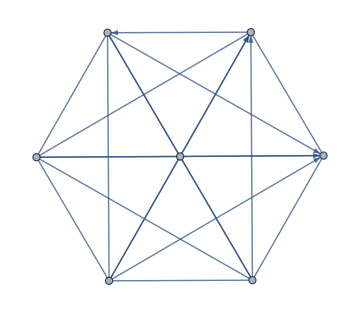

```mathematica
RandomWeightedMixedGraph[{7,21},0.5,RandomInteger[{1,7}]&,ImageSize->Medium]
```

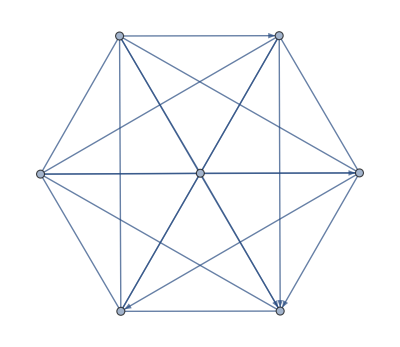
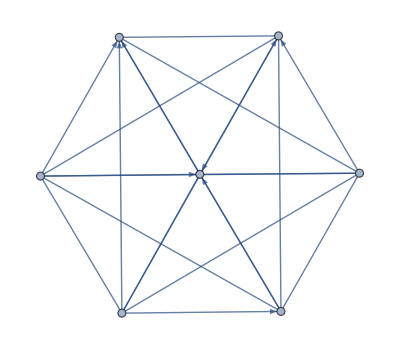
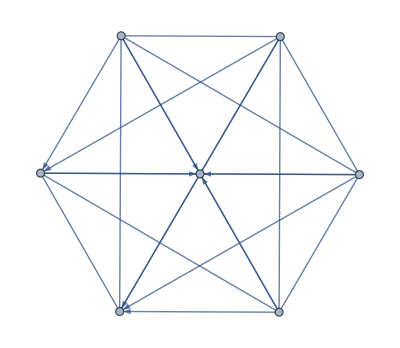

```mathematica
RandomWeightedMixedGraph[{7,21},0.5,RandomInteger[{1,7}]&,3]
```

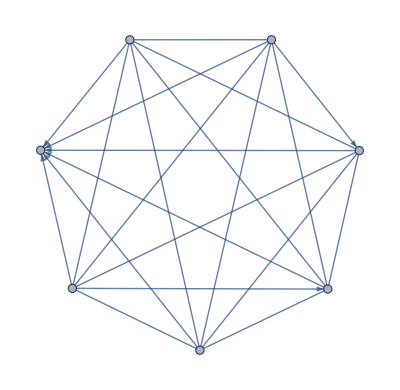

```mathematica
Select[AllTrue[VertexDegree[#],EvenQ]&][RandomWeightedMixedGraph[{7,21},0.5,RandomInteger[{1,7}]&,30]]
```

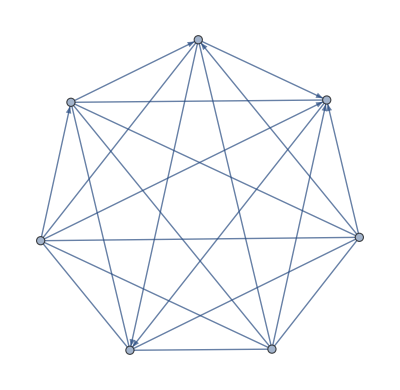

```mathematica
First[Select[AllTrue[VertexDegree[#],EvenQ]&][RandomWeightedMixedGraph[{7,21},0.5,RandomInteger[{1,7}]&,30]]]
```

This is an evenly and strongly connected graph:

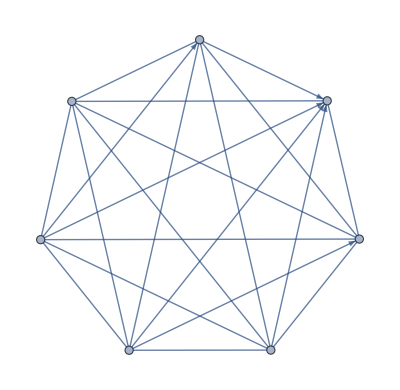

```mathematica
graph=First[Select[AllTrue[VertexDegree[#],EvenQ]&][RandomWeightedMixedGraph[{7,21},0.5,RandomInteger[{1,7}]&,30]]]
```

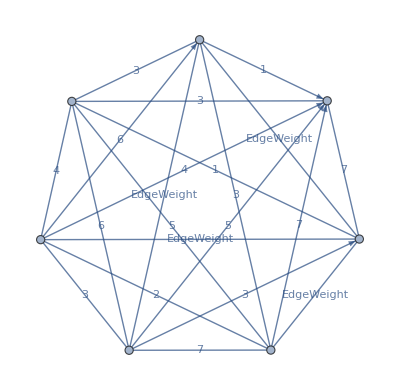

```mathematica
Graph[graph,EdgeLabels->"EdgeWeight"]
```

```mathematica
VertexDegree[graph]
```

{6,6,6,4,2,6,2}

```mathematica
AllTrue[VertexDegree[graph],EvenQ]
```

True

```mathematica
MixedGraphQ[graph]
```

True

```mathematica
EdgeWeightedGraphQ[graph]
```

True

```mathematica
ConnectedGraphQ[graph]
```

True

```mathematica
A1
```

```mathematica
EdgeList[graph,_UndirectedEdge]
```

{1<->2,1<->3,1<->4,1<->6,2<->3,2<->6,3<->6,4<->6,5<->6,5<->7,6<->7}

Arbitrarily assign a direction:

```mathematica
f@@@EdgeList[graph,_UndirectedEdge]
```

{f[1,2],f[1,3],f[1,4],f[1,6],f[2,3],f[2,6],f[3,6],f[4,6],f[5,6],f[5,7],f[6,7]}

```mathematica
List@@@EdgeList[graph,_UndirectedEdge]
```

{{1,2},{1,3},{1,4},{1,6},{2,3},{2,6},{3,6},{4,6},{5,6},{5,7},{6,7}}

```mathematica
List@@@EdgeList[graph,_UndirectedEdge]/.{{x_,y_}->RandomChoice[]}
```

```mathematica
RandomPermutation[2]
```

Cycles[{}]

```mathematica
RandomPermutation[2]
```

Cycles[{{1,2}}]

```mathematica
Permute[{1,2},Cycles[{{1,2}}]]
```

{2,1}

```mathematica
Permute[{1,2},Cycles[{{}}]]
```

{1,2}

```mathematica
Permute[{1,2},RandomPermutation[2]]
```

{1,2}

```mathematica
RandomPermutation[2,EdgeCount[graph,_UndirectedEdge]]
```

{Cycles[{{1,2}}],Cycles[{}],Cycles[{}],Cycles[{}],Cycles[{{1,2}}],Cycles[{{1,2}}],Cycles[{}],Cycles[{}],Cycles[{}],Cycles[{{1,2}}],Cycles[{{1,2}}]}

```mathematica
Thread[Permute[{{a1,a2},{b1,b2},{c1,c2}},{Cycles[{{1,2}}],Cycles[{}],Cycles[{}]}]]
```

Permute::perm: {Cycles[{{1,2}}],Cycles[{}],Cycles[{}]} is not a valid permutation.

{{a2,a1},{b1,b2},{c1,c2}}

```mathematica
Thread[f[{a,b,c},{x,y,z}]]
```

{f[a,x],f[b,y],f[c,z]}

```mathematica
Thread[f[{{a1,a2},{b1,b2},{c1,c2}},{Cycles[{{1,2}}],Cycles[{}],Cycles[{}]}]]
```

{f[{a1,a2},Cycles[{{1,2}}]],f[{b1,b2},Cycles[{}]],f[{c1,c2},Cycles[{}]]}

```mathematica
Thread[Permute[{{a1,a2},{b1,b2},{c1,c2}},{Cycles[{{1,2}}],Cycles[{}],Cycles[{}]}]]//Quiet
```

{{a2,a1},{b1,b2},{c1,c2}}

```mathematica
Thread[Permute[{{a1,a2},{b1,b2},{c1,c2}},{Cycles[{{1,2}}],Cycles[{}],Cycles[{}]}]]//Quiet
```

```mathematica
Thread[Permute[{{a1,a2},{b1,b2},{c1,c2}},RandomPermutation[2,3]]]//Quiet
```

{{a2,a1},{b1,b2},{c2,c1}}

```mathematica
Take[EdgeList[graph,_UndirectedEdge],3]
```

{1<->2,1<->3,1<->4}

```mathematica
List@@@Take[EdgeList[graph,_UndirectedEdge],3]
```

{{1,2},{1,3},{1,4}}

```mathematica
Thread[Permute[Take[EdgeList[graph,_UndirectedEdge],3],RandomPermutation[2,3]]]//Quiet
```

{2<->1,3<->1,4<->1}

```mathematica
Thread[Permute[List@@@Take[EdgeList[graph,_UndirectedEdge],3],RandomPermutation[2,3]]]//Quiet
```

{{2,1},{1,3},{1,4}}

```mathematica
DirectedEdge@@@Thread[Permute[List@@@Take[EdgeList[graph,_UndirectedEdge],3],RandomPermutation[2,3]]]//Quiet
```

{1->2,1->3,4->1}

```mathematica
DirectedEdge@@@Thread[Permute[List@@@Take[EdgeList[graph,_UndirectedEdge],3],RandomPermutation[2,3]]]//Quiet
```

{2->1,3->1,1->4}

```mathematica
DirectedEdge@@@Thread[Permute[List@@@EdgeList[graph,_UndirectedEdge],RandomPermutation[2,EdgeCount[graph,_UndirectedEdge]]]]//Quiet
```

{1->2,1->3,1->4,6->1,2->3,2->6,6->3,4->6,6->5,5->7,6->7}

This is A1:

```mathematica
EdgeList[graph,_DirectedEdge]
```

{1->7,1->5,2->5,2->7,2->4,3->4,3->7,3->5,4->7,4->5}

```mathematica
EdgeList[graph,_DirectedEdge]∪DirectedEdge@@@Thread[Permute[List@@@EdgeList[graph,_UndirectedEdge],RandomPermutation[2,EdgeCount[graph,_UndirectedEdge]]]]//Quiet
```

{1->2,1->3,1->5,1->7,2->4,2->5,2->6,2->7,3->2,3->4,3->5,3->7,4->1,4->5,4->7,5->6,5->7,6->1,6->3,6->4,6->7}

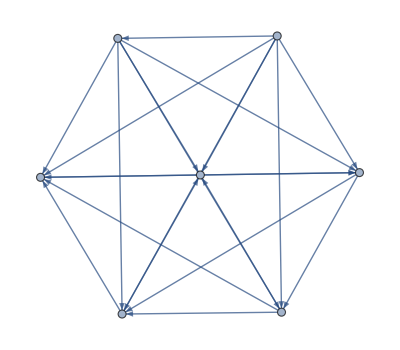

```mathematica
Graph[EdgeList[graph,_DirectedEdge]∪DirectedEdge@@@Thread[Permute[List@@@EdgeList[graph,_UndirectedEdge],RandomPermutation[2,EdgeCount[graph,_UndirectedEdge]]]]//Quiet]
```

List of edge weights

```mathematica
AnnotationValue[{graph,EdgeList[graph]},EdgeWeight]
```

{7,2,3,5,3,6,4,3,1,7,7,2,3,5,3,6,4,3,1,7,3}

```mathematica
AnnotationValue[{graph,EdgeList[graph,_UndirectedEdge]},EdgeWeight]
```

{7,2,3,5,3,6,4,3,1,7,3}

```mathematica
AnnotationValue[{graph,EdgeList[graph,_DirectedEdge]},EdgeWeight]
```

{7,2,3,5,3,6,4,3,1,7}

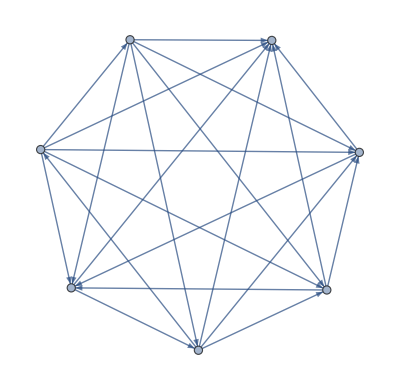

```mathematica
Graph[EdgeList[graph,_DirectedEdge]∪DirectedEdge@@@Thread[Permute[List@@@EdgeList[graph,_UndirectedEdge],RandomPermutation[2,EdgeCount[graph,_UndirectedEdge]]]]//Quiet,EdgeWeight->AnnotationValue[{graph,EdgeList[graph]},EdgeWeight]]
```

Adding the edge weight:

```mathematica
AnnotationValue[{graph,EdgeList[graph,_DirectedEdge]},EdgeWeight]
```

{7,2,3,5,3,6,4,3,1,7}

```mathematica
Join[AnnotationValue[{graph,EdgeList[graph,_DirectedEdge]},EdgeWeight],AnnotationValue[{graph,EdgeList[graph,_UndirectedEdge]},EdgeWeight]]
```

{7,2,3,5,3,6,4,3,1,7,7,2,3,5,3,6,4,3,1,7,3}

```mathematica
Join[EdgeList[graph,_DirectedEdge],DirectedEdge@@@Thread[Permute[List@@@EdgeList[graph,_UndirectedEdge],RandomPermutation[2,EdgeCount[graph,_UndirectedEdge]]]]]//Quiet
```

{1->7,1->5,2->5,2->7,2->4,3->4,3->7,3->5,4->7,4->5,2->1,1->3,1->4,6->1,2->3,6->2,3->6,6->4,5->6,7->5,7->6}

```mathematica
Thread[Quiet[Join[EdgeList[graph,_DirectedEdge],DirectedEdge@@@Thread[Permute[List@@@EdgeList[graph,_UndirectedEdge],RandomPermutation[2,EdgeCount[graph,_UndirectedEdge]]]]]]->Join[AnnotationValue[{graph,EdgeList[graph,_DirectedEdge]},EdgeWeight],AnnotationValue[{graph,EdgeList[graph,_UndirectedEdge]},EdgeWeight]]]
```

{1->7→7,1->5→2,2->5→3,2->7→5,2->4→3,3->4→6,3->7→4,3->5→3,4->7→1,4->5→7,2->1→7,1->3→2,1->4→3,1->6→5,2->3→3,2->6→6,3->6→4,6->4→3,6->5→1,7->5→7,7->6→3}

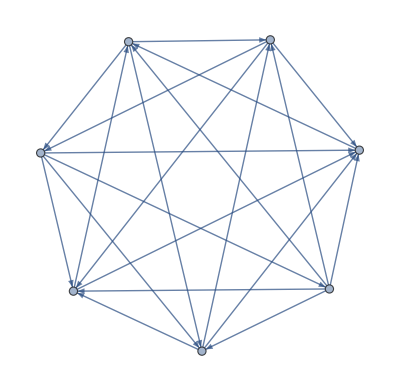

```mathematica
Graph[EdgeList[graph,_DirectedEdge]∪DirectedEdge@@@Thread[Permute[List@@@EdgeList[graph,_UndirectedEdge],RandomPermutation[2,EdgeCount[graph,_UndirectedEdge]]]]//Quiet,EdgeWeight->Thread[Quiet[Join[EdgeList[graph,_DirectedEdge],DirectedEdge@@@Thread[Permute[List@@@EdgeList[graph,_UndirectedEdge],RandomPermutation[2,EdgeCount[graph,_UndirectedEdge]]]]]]->Join[AnnotationValue[{graph,EdgeList[graph,_DirectedEdge]},EdgeWeight],AnnotationValue[{graph,EdgeList[graph,_UndirectedEdge]},EdgeWeight]]]]
```

```mathematica
RandomPermutation[2,EdgeCount[graph,_UndirectedEdge]]
```

{Cycles[{{1,2}}],Cycles[{}],Cycles[{{1,2}}],Cycles[{}],Cycles[{}],Cycles[{}],Cycles[{{1,2}}],Cycles[{{1,2}}],Cycles[{{1,2}}],Cycles[{}],Cycles[{{1,2}}]}

```mathematica
InversePermutation[{Cycles[{{1,2}}],Cycles[{}],Cycles[{{1,2}}],Cycles[{}],Cycles[{}],Cycles[{}],Cycles[{{1,2}}],Cycles[{{1,2}}],Cycles[{{1,2}}],Cycles[{}],Cycles[{{1,2}}]}]
```

PermutationPower[{Cycles[{{1,2}}],Cycles[{}],Cycles[{{1,2}}],Cycles[{}],Cycles[{}],Cycles[{}],Cycles[{{1,2}}],Cycles[{{1,2}}],Cycles[{{1,2}}],Cycles[{}],Cycles[{{1,2}}]},-1]

```mathematica
InversePermutation/@{Cycles[{{1,2}}],Cycles[{}],Cycles[{{1,2}}],Cycles[{}],Cycles[{}],Cycles[{}],Cycles[{{1,2}}],Cycles[{{1,2}}],Cycles[{{1,2}}],Cycles[{}],Cycles[{{1,2}}]}
```

{Cycles[{{1,2}}],Cycles[{}],Cycles[{{1,2}}],Cycles[{}],Cycles[{}],Cycles[{}],Cycles[{{1,2}}],Cycles[{{1,2}}],Cycles[{{1,2}}],Cycles[{}],Cycles[{{1,2}}]}